## BoundedCellVoronoi-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 11:38:17
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Generate 50 random vertices to use a Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
v=Table[{r,r}, {50}];
```

Use the Voronoi Centers to generate a tissue with 50 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[v]
```

Tissue[{{-7.70525,26.1248},{-7.36704,38.057},{-4.53679,-1.99583},{-3.7445,12.4722},{-1.29348,-4.89115},{-0.25534,52.2098},{-0.10769,82.7145},{0.2912,17.1039},{0.4161,98.2411},{1.07851,46.2167},{2.29548,86.2911},{3.15447,66.8751},{3.91052,66.0075},{3.93638,64.9559},{4.68308,102.345},{7.93707,17.5663},{8.56273,18.0353},{9.92348,68.9949},{11.2124,40.1864},{12.8907,-1.71789},{13.2204,-1.96597},{13.591,27.6706},{18.9874,88.4624},{20.3402,99.3312},{21.5356,98.0421},{21.6382,89.9882},{25.4466,27.5912},{28.0507,-1.01883},{28.7242,49.592},{28.8242,51.0846},{29.4847,48.6295},{33.1064,9.33497},{33.4409,3.70264},{34.0501,23.8662},{34.5626,12.5395},{34.85,77.8366},{34.9981,70.5841},{35.1813,104.635},{36.4362,67.5468},{40.4602,66.3621},{42.4635,-1.74547},{44.892,87.8212},{44.9533,35.5991},{45.0112,36.1632},{45.2227,35.2355},{45.7401,36.7442},{46.2356,100.22},{46.4338,14.8715},{48.0477,40.1086},{49.2813,52.202},{50.6883,103.329},{51.6478,14.7592},{52.4401,27.0815},{52.7074,-0.440134},{55.0658,11.8362},{55.2837,26.4022},{57.0282,-3.39875},{57.6868,45.1359},{57.7176,67.5981},{59.9473,103.089},{60.5331,55.4959},{61.293,43.906},{61.6157,81.8782},{63.1647,14.5848},{63.8799,35.2819},{63.9185,83.3172},{64.9249,23.2413},{64.9999,60.439},{65.4276,107.958},{65.7112,60.2809},{65.9964,17.4745},{66.7673,88.7376},{67.0283,-1.82139},{67.4368,-1.47236},{67.8257,61.6155},{69.8159,53.5558},{71.404,35.3386},{71.4536,35.3797},{72.3317,35.719},{72.3866,90.185},{74.1376,39.3951},{74.2085,75.5168},{74.6375,75.0548},{74.7461,0.797786},{75.7041,46.796},{76.2845,14.1503},{76.6474,107.248},{78.2181,87.1133},{78.2227,87.8981},{79.3775,5.46859},{79.4401,104.602},{80.5356,74.675},{81.7586,27.5803},{81.9178,74.1999},{82.989,103.727},{83.0247,4.78749},{83.5518,23.8001},{83.7558,76.2377},{84.1958,63.8525},{84.4649,77.7872},{84.5343,68.0907},{84.7157,88.4533},{85.6453,87.9767},{87.8074,88.0862},{88.0589,52.2991},{88.5672,57.6232},{89.6538,104.871},{90.6289,87.7842},{90.6686,104.25},{91.2333,7.17024},{92.0819,71.1784},{92.1096,38.5185},{94.1988,21.0638},{94.4588,10.5146},{95.8476,75.9371},{95.894,81.9252},{96.414,101.6},{97.6104,23.7202},{98.1767,62.6183},{98.4982,41.5935},{98.5118,41.8211},{98.5747,98.025},{100.169,78.9218},{100.358,37.0647},{103.292,78.6094},{104.266,79.8004},{104.404,94.9779},{104.841,64.0995},{106.148,68.7454},{106.357,91.167},{106.8,48.9221},{108.022,57.9215}},{{1,2},{1,8},{2,10},{3,4},{3,5},{4,8},{5,20},{6,10},{6,14},{7,11},{7,12},{8,16},{9,11},{9,15},{10,19},{11,23},{12,13},{13,14},{13,18},{14,30},{15,24},{16,17},{16,20},{17,22},{17,32},{18,23},{18,37},{19,22},{19,29},{20,21},{21,28},{22,27},{23,26},{24,25},{25,26},{25,38},{26,36},{27,31},{27,34},{28,33},{29,30},{29,31},{30,39},{31,44},{32,33},{32,35},{33,41},{34,35},{34,43},{35,48},{36,37},{36,42},{37,39},{38,47},{39,40},{40,50},{40,59},{41,54},{42,47},{42,63},{43,44},{43,45},{44,46},{45,48},{45,53},{46,49},{46,65},{47,51},{48,52},{49,50},{49,58},{50,61},{51,60},{52,53},{52,55},{53,56},{54,55},{54,57},{55,64},{56,65},{56,67},{57,73},{58,61},{58,62},{59,63},{59,68},{60,69},{60,72},{61,68},{62,76},{62,78},{63,66},{64,71},{64,74},{65,77},{66,72},{66,82},{67,71},{67,77},{68,70},{69,87},{70,75},{70,76},{71,86},{72,80},{73,74},{74,84},{75,83},{75,99},{76,85},{77,78},{78,79},{79,81},{79,93},{80,89},{80,91},{81,85},{81,112},{82,83},{82,88},{83,92},{84,90},{85,105},{86,90},{86,97},{87,91},{88,89},{88,92},{89,102},{90,96},{91,95},{92,94},{93,97},{93,112},{94,98},{94,101},{95,102},{95,107},{96,110},{97,113},{98,100},{98,115},{99,101},{99,106},{100,103},{100,116},{101,111},{102,103},{103,104},{104,108},{104,109},{105,106},{105,121},{106,119},{107,109},{108,116},{108,122},{109,117},{110,114},{111,115},{111,119},{112,120},{113,114},{113,118},{115,123},{116,123},{117,122},{118,124},{119,128},{120,121},{120,124},{121,131},{122,127},{123,125},{125,126},{125,129},{126,130},{127,130},{128,129},{128,132},{131,132}},{{91,112,113,117,110,90},{94,107,122,124,104,93},{117,118,162,170,153,123},{39,49,61,44,38},{135,136,147,160,142},{83,84,90,103,100,89},{124,130,139,159,163,140,125},{59,60,92,96,88,73,68},{19,18,20,43,53,27},{156,166,174,175,177,178,173,157},{85,86,100,102,108,119,97,92},{8,15,29,41,20,9},{69,74,65,64},{51,53,55,57,85,60,52},{70,71,83,72},{150,157,167,158,151},{141,142,165,166,146},{160,161,169,179,176,174,165},{88,105,116,126,101,87},{80,81,99,95},{25,46,48,39,32,24},{77,78,82,106,94,79},{145,146,156,150,149},{6,4,5,7,23,12},{26,27,51,37,33},{137,148,149,151,155,138},{48,50,64,62,49},{75,79,93,98,81,76,74},{134,133,140,164,168,171,162},{109,143,136,132,121,108},{10,11,17,19,26,16},{72,89,86,57,56},{115,129,137,131,116},{28,32,38,42,29},{127,128,132,135,141,145,148,129},{35,37,52,59,54,36},{41,42,44,63,66,70,56,55,43},{23,30,31,40,45,25,22},{111,99,98,104,125,133,114,112},{102,103,110,123,152,144,109},{46,45,47,58,77,75,69,50},{96,97,120,127,115,105},{154,152,153,172,181,180,169},{13,16,33,35,34,21,14},{119,121,128,120},{66,67,95,111,91,84,71},{143,144,154,161,147},{114,134,118,113},{61,62,65,76,80,67,63},{1,2,12,22,24,28,15,3}}]

Show the tissue and the centers

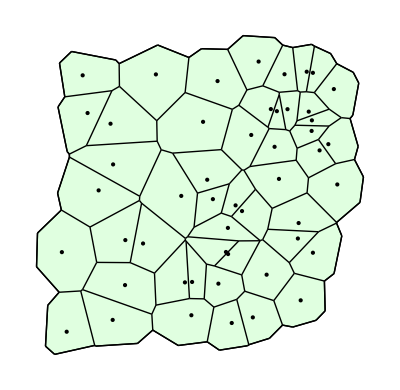

```mathematica
ShowTissue[w, Epilog-> Point/@v]
```